# Homework 1: Equivalence principle at work: charge in a lab

## 1. Uniformly accelerated charge

The trajectory of a uniformly accelerated charge in Minkowski spacetime is given by the following plots.

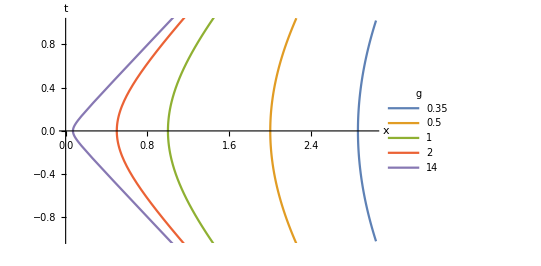

```mathematica
ParametricPlot[Evaluate@Table[{1/g Cosh[g τ],1/g Sinh[g τ]},{g,{0.35,0.5,1,2,14}}],{τ,-1,1},PlotRange->{{0,3},{-1,1}},PlotLegends->LineLegend[{0.35,0.5,1,2,14},LegendLabel->g],AxesLabel->{x,t}]
```

Let us now fix the value of the four acceleration to be some suitable parameter

```mathematica
g=2
```

2

Then the solutions of constant X are

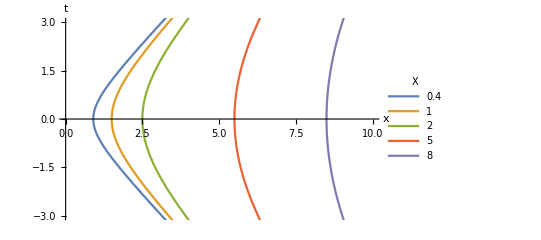

```mathematica
ParametricPlot[Evaluate@Table[{(1/g+X)Cosh[g T],(1/g+X)Sinh[g T]},{X,{0.4,1,2,5,8}}],{T,-1,1},PlotRange->{{0,10},{-3,3}},PlotLegends->LineLegend[{0.4,1,2,5,8},LegendLabel->X],AxesLabel->{x,t}]
```

while those of constant T are

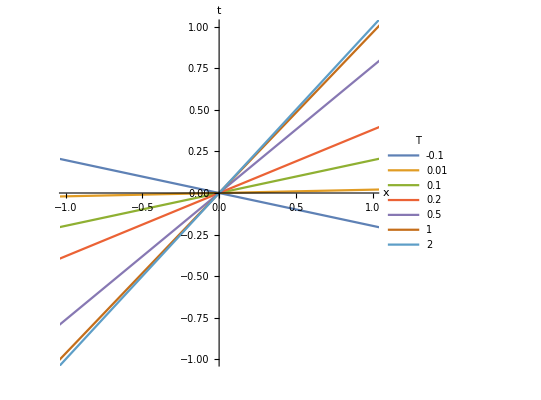

```mathematica
ParametricPlot[Evaluate@Table[{(1/g+X)Cosh[g T],(1/g+X)Sinh[g T]},{T,{-0.1,0.01,0.1,0.2,0.5,1,2}}],{X,-2,2},PlotRange->{{-1,1},{-1,1}},PlotLegends->LineLegend[{-0.1,0.01,0.1,0.2,0.5,1,2},LegendLabel->T],AxesLabel->{x,t}]
```

## 2. Field of a uniformly accelerated charge

We begin by defining our coordinates and the value of the retarded time with the corresponding position of the particle.

```mathematica
coord={t,x,ρ,ϕ};
δ=ρ^2+x^2+L^2-t^2;
ξ=√(((L^2+t^2-ρ^2-x^2)^2)/4+L^2 ρ^2);
tQ=(t δ-2 x ξ)/(2(x^2-t^2));
xQ=(x δ-2 t ξ)/(2(x^2-t^2));
```

We can now create our four potential

```mathematica
A=Q/(t xQ-x tQ){-xQ,tQ,0,0};
```

Our field strength tensor can now be defined

```mathematica
F=Table[D[A[[n]],coord[[m]]]-D[A[[m]],coord[[n]]]//FullSimplify,{m,1,4},{n,1,4}];
F//MatrixForm
```

(0 | (4 L^2 (L^2+t^2-x^2+ρ^2))/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | -(8 L^2 x ρ)/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | 0
-(4 L^2 (L^2+t^2-x^2+ρ^2))/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | 0 | (8 L^2 t ρ)/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | 0
(8 L^2 x ρ)/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | -(8 L^2 t ρ)/((L^4+2 L^2 (t^2-x^2+ρ^2)+(-t^2+x^2+ρ^2)^2)^(3/2)) | 0 | 0
0 | 0 | 0 | 0)

## 3. Sitting on the charge

```mathematica
Clear[g]
```

The modified Coulomb potential is

```mathematica
r=√(X^2+ρ^2);
Φ=Q/r (1+g X+ (g^2 r^2)/2)/(√(1+g X+ (g^2 r^2)/4));
φ:=Φ/(1+g X);
```

We normalize by the charge.

```mathematica
Q=1
```

1

Then the contour plots of the potential are the following.

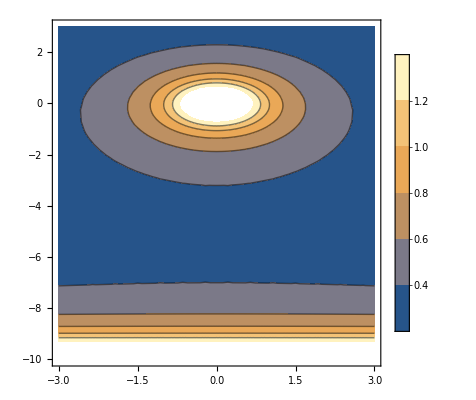
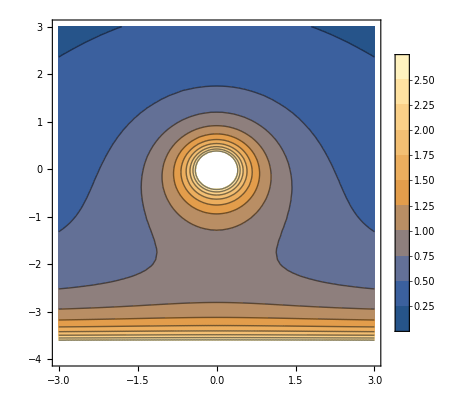
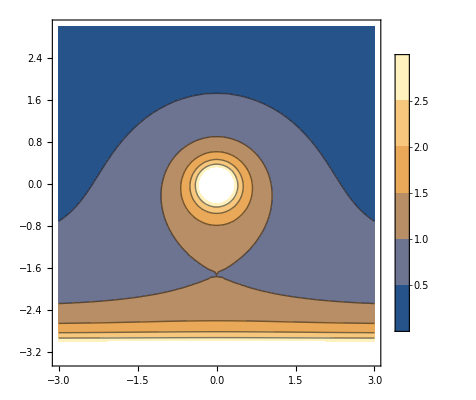
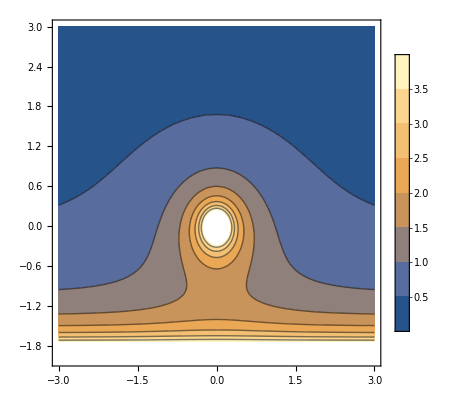
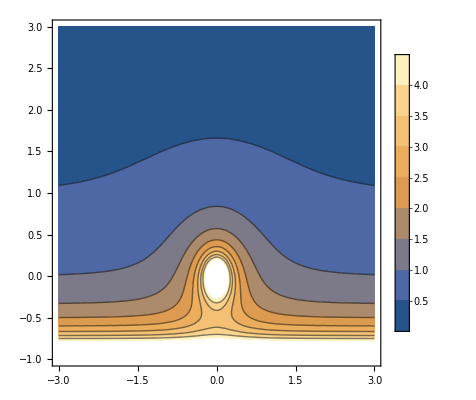

```mathematica
Table[ContourPlot[φ,{ρ,-3,3},{X,-1/g,3},PlotLegends->Automatic],{g,{0.1,0.25,0.3,0.5,1}}]
```

We can now define our new coordinates and the metric, potential and field strength in them.

```mathematica
coordp={T,X,ρ,ϕ};
gp={{-(1+g X)^2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,ρ^2}};
Ap ={-Φ,0,0,0};
Fp=Table[D[Ap[[n]],coordp[[m]]]-D[Ap[[m]],coordp[[n]]]//FullSimplify,{m,1,4},{n,1,4}] ;
```

Then our field strength is.

```mathematica
Fp//MatrixForm
```

(0 | -(4 (1+g X) (X (2+g X)-g ρ^2))/((X^2+ρ^2)^(3/2) ((2+g X)^2+g^2 ρ^2)^(3/2)) | -(8 (1+g X)^2 ρ)/((X^2+ρ^2)^(3/2) ((2+g X)^2+g^2 ρ^2)^(3/2)) | 0
(4 (1+g X) (X (2+g X)-g ρ^2))/((X^2+ρ^2)^(3/2) ((2+g X)^2+g^2 ρ^2)^(3/2)) | 0 | 0 | 0
(8 (1+g X)^2 ρ)/((X^2+ρ^2)^(3/2) ((2+g X)^2+g^2 ρ^2)^(3/2)) | 0 | 0 | 0
0 | 0 | 0 | 0)

We can quickly check that this indeed satisfies Maxwell' s equations.

```mathematica
Table[∑_(m=1)^4 D[√(-Det[gp])(Inverse[gp].Fp.Inverse[gp])[[m,n]],coordp[[m]]]//Simplify,{n,1,4}]
```

{0,0,0,0}